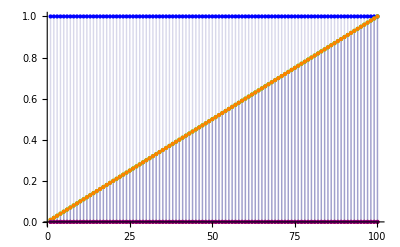

```mathematica
n=100;
Array[ PC, n];
Table[PC[i]={1,0,i/n,i/n,0},{i,1,n}];
 (* {energy, job done, Job tendancy, abilily for diffciulty, Effciency = energy/difficulty }*)
Show[
ListPlot[Table[PC[i][[1]],{i,1,n}],Filling->Axis,PlotStyle->Blue],
ListPlot[Table[PC[i][[2]],{i,1,n}],Filling->Axis,PlotStyle->Red],
ListPlot[Table[PC[i][[3]],{i,1,n}],Filling->Axis,PlotStyle->Green],
ListPlot[Table[PC[i][[4]],{i,1,n}],Filling->Axis,PlotStyle->Orange],
ListPlot[Table[PC[i][[5]],{i,1,n}],Filling->Axis,PlotStyle->Purple],
PlotRange->Automatic
]
```

{0.991225,0.260796,3.80077}

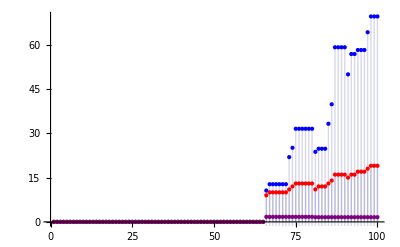

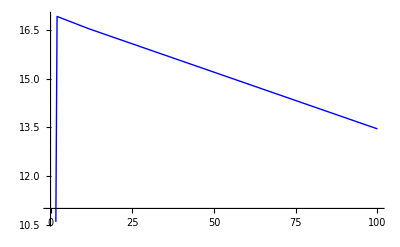

```mathematica
(* Dispaly  *)
{Job0eng,Job0diff,eff}
Table[PC[i],{i,1,n}];
Count[Table[PC[i],{i,1,n}],{0,0,0,0,0}];
{Mean[Table[PC[i][[1]],{i,1,n}]],StandardDeviation[Table[PC[i][[1]],{i,1,n}]]};
{Mean[Table[PC[i][[3]],{i,1,n}]],StandardDeviation[Table[PC[i][[3]],{i,1,n}]]};
{Mean[Table[PC[i][[5]],{i,1,n}]],StandardDeviation[Table[PC[i][[5]],{i,1,n}]]};
Show[
ListPlot[Table[PC[i][[1]],{i,1,n}],Filling->Axis,PlotStyle->Blue],(* energy*)
ListPlot[Table[PC[i][[2]],{i,1,n}],Filling->Axis,PlotStyle->Red],(* # job done*)
ListPlot[Table[PC[i][[3]],{i,1,n}],Filling->Axis,PlotStyle->Green], (* tendancy*)
ListPlot[Table[PC[i][[5]],{i,1,n}],Filling->Axis,PlotStyle->Purple](* eff*)
]
Show[
ListPlot[Table[St[i][[1]],{i,1,100}],Joined->True,PlotStyle->Blue],
ListPlot[Table[St[i][[2]],{i,1,100}],Joined->True,PlotStyle->Red],
ListPlot[Table[St[i][[3]],{i,1,100}],Joined->True,PlotStyle->Green]
]
```

```mathematica
R=10; (* reward ratio of each job *)
```

```mathematica
Array[St,100];
turn=0;
Table[St[i]={0,0,0},{i,1,100}];
```

```mathematica
Do[
Job0eng=Random[];
Job0diff=Random[];
eff=Job0eng/Job0diff;
turn=turn+1;
(* energy used *)
Table[PC[i]=PC[i]-{0.1,0,0,0,0},{i,1,n}];
(* doing Job *)
Table[
{If[(Job0eng < PC[i][[3]] &&PC[i][[4]] > Job0diff)&& PC[i][[1]]>0,
PC[i]=PC[i]+{Job0eng*R,1,0,0,0},
0],
(* Changing Job tendancy, +0.1 , due to last job efficiency*)
If[eff>PC[i][[5]] && 0≤ PC[i][[3]]≤1 &&PC[i][[4]] > Job0diff,
PC[i]=PC[i]+{0,0,0.1,0,0.1},
PC[i]=PC[i]-{0,0,0.2,0,0}]},
{i,1,n}];
(* Set die *)
Table[
If[PC[i][[1]]≤0,
PC[i]={0,0,0,0,0},
PC[i]],
{i,1,n}];
St[turn]={Mean[Table[PC[i][[1]],{i,1,n}]],Mean[Table[PC[i][[3]],{i,1,n}]],Mean[Table[PC[i][[5]],{i,1,n}]]},
{turn,1,100}]
```

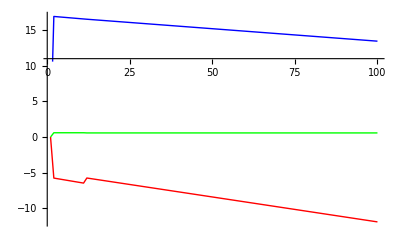

```mathematica
Show[
ListPlot[Table[St[i][[1]],{i,1,100}],Joined->True,PlotStyle->Blue], (* mean energy *)
ListPlot[Table[St[i][[2]],{i,1,100}],Joined->True,PlotStyle->Red], (* mean job tendency *)
ListPlot[Table[St[i][[3]],{i,1,100}],Joined->True,PlotStyle->Green],(* mean effecicey *)
PlotRange->All
]
```